```mathematica
Quit[];
```

```mathematica
σ = 0.35;
ρ = 0.6;
incomeProcess = ARProcess[{ρ}, σ(1-ρ^2)^(1/2)]
```

ARProcess[{0.6},0.28]

```mathematica
Mean[incomeProcess[t]]
```

0

```mathematica
Variance[incomeProcess[t]]
```

0.4375

```mathematica
data=RandomFunction[incomeProcess,{1,10^3}];
```

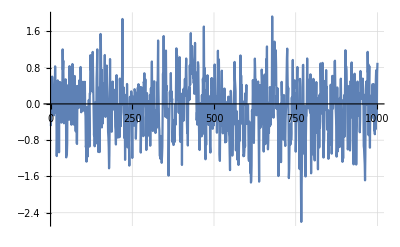

```mathematica
ListLinePlot[data, GridLines->Automatic]
```

```mathematica
DiscretePlot3D[CovarianceFunction[incomeProcess,s,t],{s,0,10},{t,0,10},ExtentSize->1/2,ColorFunction->"Rainbow"]
```

-Graphics3D-